## Structural complexity of functional response models - Part 2

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/general-functional-responses/code/Mathematica

### Preliminaries

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1)
The first term is the likelihood. 
The second term is dependent on parameter count (k) and sample size (n).
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.
The flexibility term by itself can only be compared between models having the same number of parameters.

#### Load results of "FisherMatrix-1_Compute.nb”

Pick the output that has been successfully computed :

```mathematica
Get["results/FisherMatrix-1_Output_FIM_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_aNInt_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_NInt_k1k2k3"];
```

### Second Term dependence on k and n

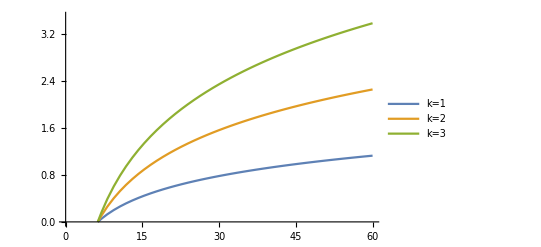
-Graphics-Sample size (n)Parameter complexity

```mathematica
AltLabel1="k";
p1=Labeled[Plot[Evaluate@Table[k/2 Log[n/(2 π)],{k,1,3}],{n,1,60},
PlotLegends->Placed[{"k=1","k=2","k=3"},Above],PlotRange->{{0,60},{0,3.5}}],
{Style["Sample size (n)"],Style["Parameter complexity"]},{Bottom,Left},
RotateLabel->True,
Spacings->{1, 0},
BaseStyle->{FontFamily->"Arial",12},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_ParameterComplexity.pdf",p1];
```

### Third term - Flexibility - Non-truncated λ

```mathematica
NInts={NIntH1,NIntR,NIntHV,NIntH2,NIntAG,NIntBD,NIntCM,NIntAA}
Labels={"H1","LR","HV","H2","AG","BD","CM","AA"};
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
(* Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}]; *)
```

{5.89629,5.40587,10.1498,9.3842,8.69591,11.8486,12.1909,13.0002}

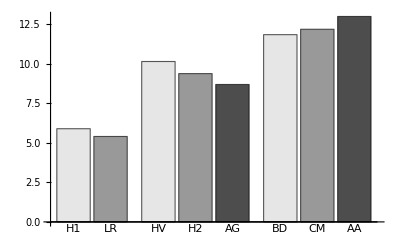
-Graphics-ModelFlexibility

```mathematica
AltLabel2="LN∫_Θ √(det  I (θ))ⅆθ";
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=Labeled[BarChart[lNInts,ChartStyle->{GrayLevel[0.9],GrayLevel[0.6],GrayLevel[0.3]}],
{Style["Model"],Style["Flexibility"]},{Bottom,Left},
RotateLabel->True,
Spacings->{0.4, 1},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_Complexity_absolute_NonTrunc.eps",bc1];
```

### Third term - Flexibility - Truncated λ

```mathematica
NInts={NIntH1Trunc,NIntRTrunc,NIntHVTrunc,NIntH2Trunc,NIntAGTrunc,NIntBDTrunc,NIntCMTrunc,NIntAATrunc}
Labels={"H1","LR","HV","H2","AG","BD","CM","AA"};
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
(* Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}]; *)
```

{2.73243,2.66231,4.15322,3.29263,3.53562,0.857961,2.64874,4.92636}

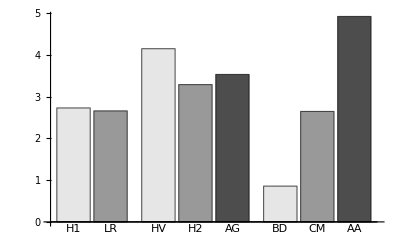
-Graphics-ModelFlexibility

```mathematica
AltLabel2="LN∫_Θ √(det  I (θ))ⅆθ";
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=Labeled[BarChart[lNInts,ChartStyle->{GrayLevel[0.9],GrayLevel[0.6],GrayLevel[0.3]}],
{Style["Model"],Style["Flexibility"]},{Bottom,Left},
RotateLabel->True,
Spacings->{0.4, 1},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_Complexity_absolute_Trunc.pdf",bc1];
```

### Partial numeric Integration - Truncated λ

Fix ' a', integrate square root of Expected Fisher Information Matrix over remaining parameters , and take natural log.

Observe that the breaks occur at Max[Νvals]/PΝprods where PΝprods is the pairwise products of all Ν and P
Also, that aNIntH1Trunc =aNIntRTrunc  = 0 for a > Max[Νvals]/Min[PΝprods].  In the given design, Min[PΝprods] = 1x2=2 and Max[Νvals] = 256.

```mathematica
PΝprods=Sort[DeleteDuplicates[Join@@Outer[Times,Pvals,Νvals]]]
```

{2,4,8,10,16,20,32,40,64,80,160}

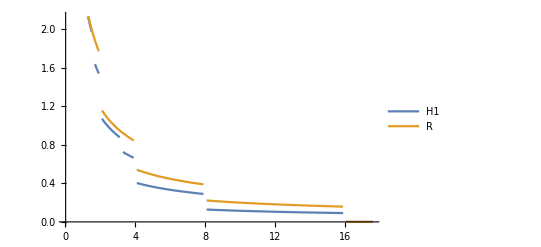

```mathematica
pnk1T=Plot[{
aNIntH1Trunc,
aNIntRTrunc
},
{a,0.01,Max[Max[Νvals]/PΝprods]*1.1},
MaxRecursion->2,
PerformanceGoal->10,
PlotLegends->Placed[{"H1","LR"},Above]]
```

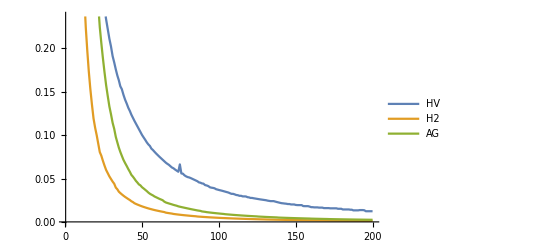

```mathematica
pnk2T=Plot[{
aNIntHVTrunc[a],
aNIntH2Trunc[a],
aNIntAGTrunc[a]
},
{a,0.1,200},
MaxRecursion->2,
PerformanceGoal->1,
PlotLegends->Placed[{"HV","H2","AG"},Above]]
```

Discontinuities also occur at Max[Νvals]/PΝprods

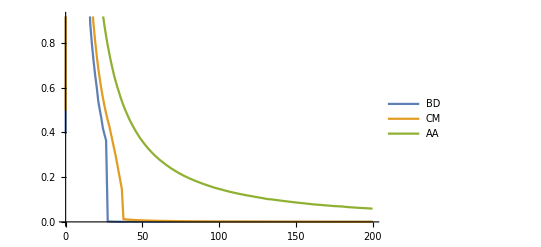

```mathematica
pnk3T=Plot[{
aNIntBDTrunc[a],
aNIntCMTrunc[a],
aNIntAATrunc[a]
},
{a,0.01,200},
MaxRecursion->2,
PerformanceGoal->1,
PlotLegends->Placed[{"BD","CM","AA"},Above]]
```

Note that the barplot *seems* to differ from the the following for k = 3 in that the barchart implies AA > CM but the plot as a function of a suggests CM > AA.  This is due to the fact that AA >> CM for very small values of a, as well as for large values of a.  It’s only at intermediate values (evident in the functional plot) that CM>AA.  In other words, the barchart is correct.

```mathematica
Α=0.001;
{aNIntBDTrunc[Α],
aNIntCMTrunc[Α],
aNIntAATrunc[Α]}
```

{0.0234033,0.0274577,0.0585579}

```mathematica
Α=50;
{aNIntBDTrunc[Α],
aNIntCMTrunc[Α],
aNIntAATrunc[Α]}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.000473537,0.00690887,0.360261}

```mathematica
Α=150;
{aNIntBDTrunc[Α],
aNIntCMTrunc[Α],
aNIntAATrunc[Α]}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.0000215594,0.000936,0.0867576}

```mathematica
pnT=Labeled[GraphicsRow[{pnk1T,pnk2T,pnk3T},ImageSize->Large],{Style["Attack rate"],Style["LN∫_Θ √(det  I (θ))ⅆθ"]},{Bottom,Left},RotateLabel->True,Spacings->{3, 0},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"}]
Export["results/FisherMatrix-2_Output_partial_numeric_a_Trunc.pdf",pnT];
```

-Graphics-Attack rateLN∫_Θ √(det  I (θ))ⅆθ

### Partial numeric Integration - Non-truncated λ

Fix ' a', integrate square root of Expected Fisher Information Matrix over remaining parameters , and take natural log.

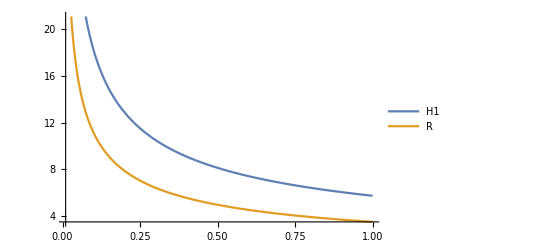

```mathematica
ParmRangeB=Drop[ParmRangeA,1];
precgoal=2;
pnk1=Plot[{
aNIntH1,
aNIntR
},
{a,0.01,1},
PlotLegends->Placed[{"H1","LR"},Above]]
```

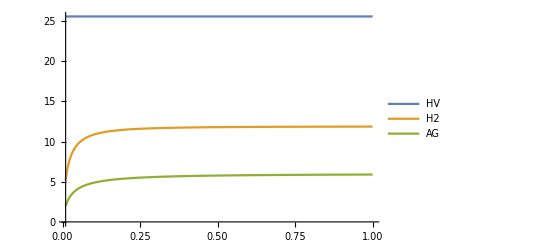

```mathematica
pnk2=Plot[{
aNIntHV,
aNIntH2[a],
aNIntAG[a]
},
{a,0.01,1},
PlotLegends->Placed[{"HV","H2","AG"},Above]]
```

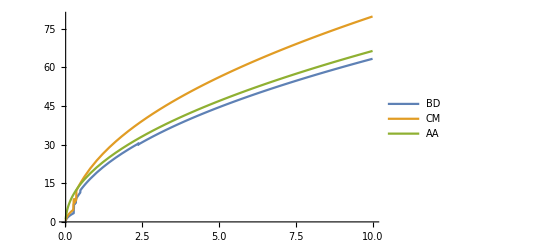

```mathematica
pnk3=Plot[{
aNIntBD[a],
aNIntCM[a],
aNIntAA[a]
},
{a,0.01,10},
PlotLegends->Placed[{"BD","CM","AA"},Above]]
```

```mathematica
pn=Labeled[GraphicsRow[{pnk1,pnk2,pnk3},ImageSize->Large],{Style["Attack rate"],Style["LN∫_Θ √(det  I (θ))ⅆθ"]},{Bottom,Left},RotateLabel->True,Spacings->{3, 0},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"}]
Export["results/FisherMatrix-2_Output_partial_numeric_a_NonTrunc.pdf",pn];
```

-Graphics-Attack rateLN∫_Θ √(det  I (θ))ⅆθ

## Investigate better cut - points to avoid singularities

```mathematica
Νvals
```

{2,4,8,16,32}

```mathematica
Pvals
```

{1,2,5}

```mathematica
Factor[DetH1Trunc]
```

1/(15 a)2 (Boole[0≤2 a≤32]+4 Boole[0≤4 a≤32]+8 Boole[0≤8 a≤32]+5 Boole[0≤10 a≤32]+16 Boole[0≤16 a≤32]+10 Boole[0≤20 a≤32]+32 Boole[0≤32 a≤32]+20 Boole[0≤40 a≤32]+32 Boole[0≤64 a≤32]+40 Boole[0≤80 a≤32]+80 Boole[0≤160 a≤32])

```mathematica
Factor[DetRTrunc]
```

1/(5 a)2 (Boole[0≤2 a≤32]+2 Boole[0≤4 a≤32]+4 Boole[0≤8 a≤32]+8 Boole[0≤16 a≤32]+16 Boole[0≤32 a≤32])

```mathematica
Factor[DetHVTrunc]
```

1/9 2^(2-m) 5^(-2-m) (2 5^m Boole[0≤2 a≤32] Boole[0≤2^(2-m) a≤32] Log[2]^2+4 5^m Boole[0≤4 a≤32] Boole[0≤2^(2-m) a≤32] Log[2]^2+8 5^m Boole[0≤8 a≤32] Boole[0≤2^(2-m) a≤32] Log[2]^2+16 5^m Boole[0≤16 a≤32] Boole[0≤2^(2-m) a≤32] Log[2]^2+32 5^m Boole[0≤32 a≤32] Boole[0≤2^(2-m) a≤32] Log[2]^2+4 5^m Boole[0≤2 a≤32] Boole[0≤2^(3-m) a≤32] Log[2]^2+8 5^m Boole[0≤4 a≤32] Boole[0≤2^(3-m) a≤32] Log[2]^2+16 5^m Boole[0≤8 a≤32] Boole[0≤2^(3-m) a≤32] Log[2]^2+32 5^m Boole[0≤16 a≤32] Boole[0≤2^(3-m) a≤32] Log[2]^2+64 5^m Boole[0≤32 a≤32] Boole[0≤2^(3-m) a≤32] Log[2]^2+8 5^m Boole[0≤2 a≤32] Boole[0≤2^(4-m) a≤32] Log[2]^2+16 5^m Boole[0≤4 a≤32] Boole[0≤2^(4-m) a≤32] Log[2]^2+32 5^m Boole[0≤8 a≤32] Boole[0≤2^(4-m) a≤32] Log[2]^2+64 5^m Boole[0≤16 a≤32] Boole[0≤2^(4-m) a≤32] Log[2]^2+128 5^m Boole[0≤32 a≤32] Boole[0≤2^(4-m) a≤32] Log[2]^2+16 5^m Boole[0≤2 a≤32] Boole[0≤2^(5-m) a≤32] Log[2]^2+32 5^m Boole[0≤4 a≤32] Boole[0≤2^(5-m) a≤32] Log[2]^2+64 5^m Boole[0≤8 a≤32] Boole[0≤2^(5-m) a≤32] Log[2]^2+128 5^m Boole[0≤16 a≤32] Boole[0≤2^(5-m) a≤32] Log[2]^2+256 5^m Boole[0≤32 a≤32] Boole[0≤2^(5-m) a≤32] Log[2]^2+32 5^m Boole[0≤2 a≤32] Boole[0≤2^(6-m) a≤32] Log[2]^2+64 5^m Boole[0≤4 a≤32] Boole[0≤2^(6-m) a≤32] Log[2]^2+128 5^m Boole[0≤8 a≤32] Boole[0≤2^(6-m) a≤32] Log[2]^2+256 5^m Boole[0≤16 a≤32] Boole[0≤2^(6-m) a≤32] Log[2]^2+512 5^m Boole[0≤32 a≤32] Boole[0≤2^(6-m) a≤32] Log[2]^2+10 Boole[0≤2^(2-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2]^2+20 Boole[0≤2^(3-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2]^2+40 Boole[0≤2^(4-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2]^2+80 Boole[0≤2^(5-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2]^2+160 Boole[0≤2^(6-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2]^2+20 Boole[0≤2^(2-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2]^2+40 Boole[0≤2^(3-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2]^2+80 Boole[0≤2^(4-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2]^2+160 Boole[0≤2^(5-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2]^2+320 Boole[0≤2^(6-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2]^2+40 Boole[0≤2^(2-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2]^2+80 Boole[0≤2^(3-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2]^2+160 Boole[0≤2^(4-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2]^2+320 Boole[0≤2^(5-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2]^2+640 Boole[0≤2^(6-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2]^2+80 Boole[0≤2^(2-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2]^2+160 Boole[0≤2^(3-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2]^2+320 Boole[0≤2^(4-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2]^2+640 Boole[0≤2^(5-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2]^2+1280 Boole[0≤2^(6-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2]^2+160 Boole[0≤2^(2-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2]^2+320 Boole[0≤2^(3-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2]^2+640 Boole[0≤2^(4-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2]^2+1280 Boole[0≤2^(5-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2]^2+2560 Boole[0≤2^(6-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2]^2-20 Boole[0≤2^(2-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2] Log[5]-40 Boole[0≤2^(3-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2] Log[5]-80 Boole[0≤2^(4-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2] Log[5]-160 Boole[0≤2^(5-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2] Log[5]-320 Boole[0≤2^(6-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[2] Log[5]-40 Boole[0≤2^(2-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2] Log[5]-80 Boole[0≤2^(3-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2] Log[5]-160 Boole[0≤2^(4-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2] Log[5]-320 Boole[0≤2^(5-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2] Log[5]-640 Boole[0≤2^(6-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[2] Log[5]-80 Boole[0≤2^(2-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2] Log[5]-160 Boole[0≤2^(3-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2] Log[5]-320 Boole[0≤2^(4-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2] Log[5]-640 Boole[0≤2^(5-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2] Log[5]-1280 Boole[0≤2^(6-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[2] Log[5]-160 Boole[0≤2^(2-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2] Log[5]-320 Boole[0≤2^(3-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2] Log[5]-640 Boole[0≤2^(4-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2] Log[5]-1280 Boole[0≤2^(5-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2] Log[5]-2560 Boole[0≤2^(6-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[2] Log[5]-320 Boole[0≤2^(2-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2] Log[5]-640 Boole[0≤2^(3-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2] Log[5]-1280 Boole[0≤2^(4-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2] Log[5]-2560 Boole[0≤2^(5-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2] Log[5]-5120 Boole[0≤2^(6-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[2] Log[5]+5 2^m Boole[0≤2 a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+5 2^(1+m) Boole[0≤4 a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+5 2^(2+m) Boole[0≤8 a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+5 2^(3+m) Boole[0≤16 a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+5 2^(4+m) Boole[0≤32 a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+10 Boole[0≤2^(2-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+20 Boole[0≤2^(3-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+40 Boole[0≤2^(4-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+80 Boole[0≤2^(5-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+160 Boole[0≤2^(6-m) a≤32] Boole[0≤2 5^(1-m) a≤32] Log[5]^2+5 2^(1+m) Boole[0≤2 a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+5 2^(2+m) Boole[0≤4 a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+5 2^(3+m) Boole[0≤8 a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+5 2^(4+m) Boole[0≤16 a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+5 2^(5+m) Boole[0≤32 a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+20 Boole[0≤2^(2-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+40 Boole[0≤2^(3-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+80 Boole[0≤2^(4-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+160 Boole[0≤2^(5-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+320 Boole[0≤2^(6-m) a≤32] Boole[0≤4 5^(1-m) a≤32] Log[5]^2+5 2^(2+m) Boole[0≤2 a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+5 2^(3+m) Boole[0≤4 a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+5 2^(4+m) Boole[0≤8 a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+5 2^(5+m) Boole[0≤16 a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+5 2^(6+m) Boole[0≤32 a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+40 Boole[0≤2^(2-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+80 Boole[0≤2^(3-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+160 Boole[0≤2^(4-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+320 Boole[0≤2^(5-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+640 Boole[0≤2^(6-m) a≤32] Boole[0≤8 5^(1-m) a≤32] Log[5]^2+5 2^(3+m) Boole[0≤2 a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+5 2^(4+m) Boole[0≤4 a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+5 2^(5+m) Boole[0≤8 a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+5 2^(6+m) Boole[0≤16 a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+5 2^(7+m) Boole[0≤32 a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+80 Boole[0≤2^(2-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+160 Boole[0≤2^(3-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+320 Boole[0≤2^(4-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+640 Boole[0≤2^(5-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+1280 Boole[0≤2^(6-m) a≤32] Boole[0≤16 5^(1-m) a≤32] Log[5]^2+5 2^(4+m) Boole[0≤2 a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+5 2^(5+m) Boole[0≤4 a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+5 2^(6+m) Boole[0≤8 a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+5 2^(7+m) Boole[0≤16 a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+5 2^(8+m) Boole[0≤32 a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+160 Boole[0≤2^(2-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+320 Boole[0≤2^(3-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+640 Boole[0≤2^(4-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+1280 Boole[0≤2^(5-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2+2560 Boole[0≤2^(6-m) a≤32] Boole[0≤32 5^(1-m) a≤32] Log[5]^2)

```mathematica
Factor[DetH2Trunc]
```

(32 a^2 (Boole[0≤(2 a)/(1+2 a h)≤32] Boole[0≤(4 a)/(1+4 a h)≤32]+898+26843545600 a^9 h^9 1 Boole[0≤1≤32]))/(225 (1+2 a h)^3 (1+4 a h)^3 (1+8 a h)^3 (1+16 a h)^3 (1+32 a h)^3)
 |  |  |  |

```mathematica
Solve[(2 a)/(1+2 a h)==8,h]
Solve[(2 a)/(1+2 a h)==8,a]
```

{{h→(-4+a)/(8 a)}}

{{a→-4/(-1+8 h)}}

## Compare non-truncated and truncated Sqrt(Det(FIM)) before integrating over parameters

```mathematica
DetH1NoTrunc=DetEFisherTrunc[FisherH1Poiss,H1,0,Infinity,subs];
```

NOTE: If we don’t truncate things then everything is identical, but things definitely change upon reducing λmax to Max[Nvals].

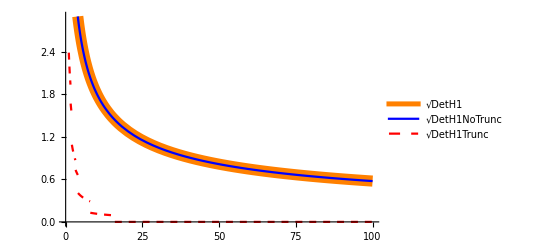

```mathematica
pH1=Plot[{Sqrt[DetH1],Sqrt[DetH1NoTrunc],Sqrt[DetH1Trunc]},{a,0,100},
PlotStyle->{{Orange,Thickness[0.02]},{Blue},{Red,Dashed}},
PlotLegends->"Expressions"]
```

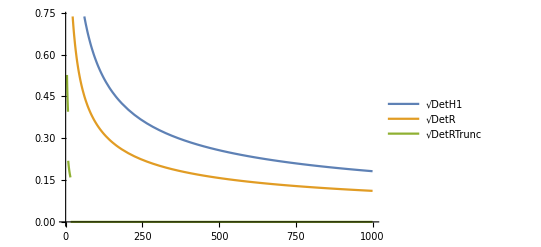

```mathematica
pR=Plot[{Sqrt[DetH1],Sqrt[DetR],Sqrt[DetRTrunc]},{a,0,1000},
PlotLegends->"Expressions"]
```

```mathematica
p3Dk1=GraphicsColumn[{pH1,pR},ImageSize->Large];
Export["results/FisherMatrix-2_Output_preIntegration-3Dk1.jpeg",p3Dk1];
```

```mathematica
pHV=Plot3D[{Sqrt[DetHV],Sqrt[DetHVTrunc]},{a,0,10},{m,0,5},AxesLabel->Automatic,
PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
pH2=Plot3D[{Sqrt[DetH2],Sqrt[DetH2Trunc]},{a,0,10},{h,0,5},AxesLabel->Automatic,
PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
pAG=Plot3D[{Sqrt[DetAG],Sqrt[DetAGTrunc]},{a,0,10},{h,0,5},AxesLabel->Automatic,
PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
p3Dk2=GraphicsColumn[{pHV,pH2,pAG},ImageSize->Large];
Export["results/FisherMatrix-2_Output_preIntegration-3Dk2.jpeg",p3Dk2];
```